```mathematica
(*85microm exp1 video:7058*)
collateral85Exp1Top={0,0,0,0,0,1,1,0,1,0};
vCentral85Exp1={14,10,11,11,11,10,10,12,11,None};
collateral85Exp1Bottom={0,1,1,0,1,1,1,0,1,0};
nbGoutteCollateralTop85Exp1Top={2,3,3,3,2,3,3,2,3,2};
nbGoutteCentral85Exp1={2,3,3,2,2,2,2,2,3,1};
nbGoutteCollateralBottom85Exp1Bottom={3,3,3,2,2,3,3,1,3,3};

(*85microm exp2 video:7063*)
collateral85Exp2Top={1,1,0,0,1,1,1,1,1,0};
vCentral85Exp2={8,7,7,8,7,7,8,8,8,7};
collateral85Exp2Bottom={0,0,0,0,1,1,1,1,1,1};
nbGoutteCollateralTop85Exp2Top={3,3,3,3,3,3,3,3,3,3};
nbGoutteCentral85Exp2={3,3,3,3,3,3,3,3,3,3};
nbGoutteCollateralBottom85Exp2Bottom={3,3,3,3,3,3,3,3,3,3};

(*85microm exp3 video:7066*)
collateral85Exp3Top={0,0,0,0,0,0,0,0,0,0};
vCentral85Exp3={9,9,9,9,9,9,10,9,9,9};
collateral85Exp3Bottom={0,0,0,0,0,1,0,0,1,0};
nbGoutteCollateralTop85Exp3Top={2,2,1,2,1,2,2,2,2,2};
nbGoutteCentral85Exp3={2,2,2,2,2,2,2,2,2,2};
nbGoutteCollateralBottom85Exp3Bottom={1,1,2,2,2,2,2,2,2,1};

(*130microm exp1 video:7050*)
collateral130Exp1Top={0,1,0,0,0,0,0,0,0,0,0};
vCentral130Exp1={13,13,14,14,10,10,14,10,9,14,14};
collateral130Exp1Bottom={0,0,0,0,0,1,0,0,1,0,0};
nbGoutteCollateralTop130Exp1Top={2,3,2,2,2,2,2,2,3,2,2};
nbGoutteCentral130Exp1={2,2,2,2,3,3,2,3,3,2,2};
nbGoutteCollateralBottom130Exp1Bottom={2,2,2,2,3,3,2,2,3,2,2};

(*130microm exp2 video:7053*)
collateral130Exp2Top={0,0,1,1,1,1,1,1,0,1};
vCentral130Exp2={7,7,8,7,7,7,7,7,7,7};
collateral130Exp2Bottom={0,1,0,1,1,1,1,0,1,1};
nbGoutteCollateralTop130Exp2Top={2,2,3,3,3,3,3,3,2,3};
nbGoutteCentral130Exp2={3,3,2,3,2,3,3,3,3,3};
nbGoutteCollateralBottom130Exp2Bottom={3,3,3,3,3,3,3,2,3,3};

(*130microm exp3 video:7057*)
collateral130Exp3Top={0,0,0,0,0,0,0,0,0,0,0};
vCentral130Exp3={13,12,13,13,14,13,13,13,11,6,13};
collateral130Exp3Bottom={0,0,0,0,0,0,0,0,0,0,0};
nbGoutteCollateralTop130Exp3Top={2,2,2,2,2,2,2,2,2,3,2};
nbGoutteCentral130Exp3={2,2,2,2,2,2,2,2,2,2,2};
nbGoutteCollateralBottom130Exp3Bottom={3,2,2,2,2,2,2,2,3,2,2};
Needs["MaTeX`"];

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm}"}];

blue=RGBColor[0.368417,0.506779,0.709798];
red=RGBColor[0.880722,0.611041,0.142051];
```

Coverslip [μm] | Replicate | N | Mean [V] | Std [V] | Min [V] | Max [V]
85 | 1 | 9 | 11.11 | 1.27 | 10.00 | 14.00
85 | 2 | 10 | 7.50 | 0.53 | 7.00 | 8.00
85 | 3 | 10 | 9.10 | 0.32 | 9.00 | 10.00
130 | 1 | 11 | 12.27 | 2.05 | 9.00 | 14.00
130 | 2 | 10 | 7.10 | 0.32 | 7.00 | 8.00
130 | 3 | 11 | 12.18 | 2.18 | 6.00 | 14.00

Coverslip [μm] | N | Mean [V] | Std [V] | Median [V] | Min [V] | Max [V]
85 | 29 | 9.17 | 1.67 | 9.00 | 7.00 | 14.00
130 | 32 | 10.63 | 2.96 | 11.50 | 6.00 | 14.00

Coverslip [μm] | N valid wells | N parasitic fusions | Probability [%]
85 | 54 | 24 | 44.4
130 | 64 | 17 | 26.6

Coverslip | N | -Graphics- | -Graphics-
85 μm | 29 | 853.16 | 96.58
130 μm | 32 | 1025.64 | 232.02

Coverslip | N | Mean [V] | Std [V] | Median [V] | Min [V] | Max [V] | -Graphics- | Parasitic fusion [%]
85 μm | 29 | 9.17 | 1.67 | 9.00 | 7 | 14 | 853.16 | 44.4
130 μm | 32 | 10.63 | 2.96 | 11.50 | 6 | 14 | 1025.64 | 26.6

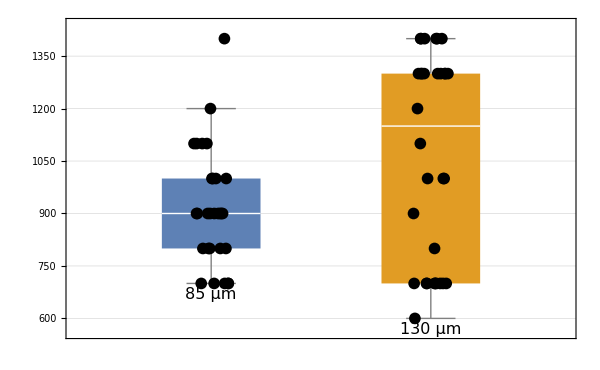

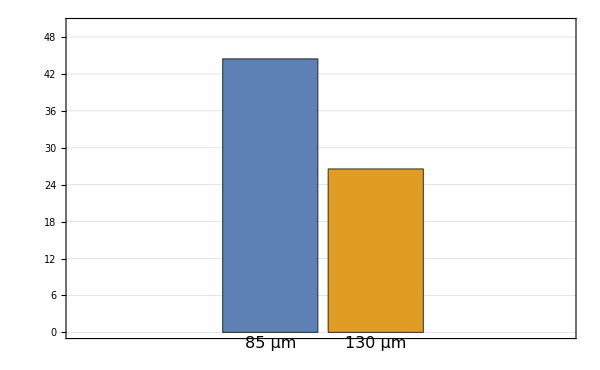

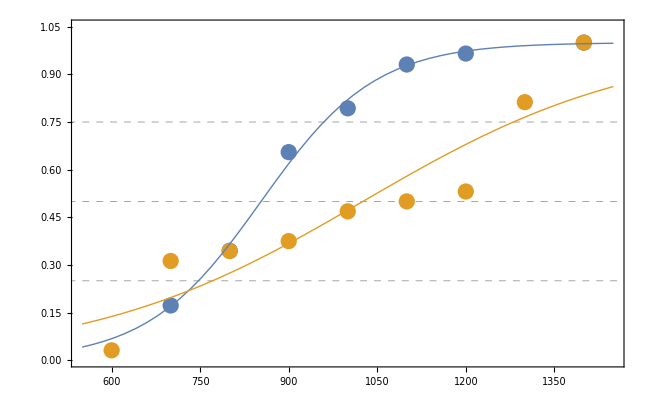

```mathematica
(* ================================================================*)(*ANALYSE COMPLETE DE L'ELECTRO-COALESCENCE*)(*Coverslips 85 µm et 130 µm*)(* ================================================================*)(* ================================================================*)(*1. ENCODAGE DES DONNEES*)(* ================================================================*)makeRawGrid[topColl_,topNDrops_,centerV_,centerNDrops_,botColl_,botNDrops_]:=Table[Module[{nDrop,vVal,mergedVal},Switch[i,(*----------------TOP----------------*)1,nDrop=topNDrops[[j]];
mergedVal=If[nDrop>1,TrueQ[topColl[[j]]==1],Missing["SingleDroplet"]];
<|"N_drops"->nDrop,"Merged"->mergedVal|>,(*---------------CENTER--------------*)2,nDrop=centerNDrops[[j]];
vVal=centerV[[j]];
vVal=If[nDrop>1&&NumericQ[vVal],vVal,Missing["SingleDropletOrNoFusion"]];
<|"N_drops"->nDrop,"Voltage"->vVal|>,(*---------------BOTTOM--------------*)3,nDrop=botNDrops[[j]];
mergedVal=If[nDrop>1,TrueQ[botColl[[j]]==1],Missing["SingleDroplet"]];
<|"N_drops"->nDrop,"Merged"->mergedVal|>]],{i,1,3},{j,1,Length[centerV]}];

formatExperiment[coverslip_Integer,replicate_Integer,gridData_List]:=Module[{rows,cols},{rows,cols}=Dimensions[gridData];
Flatten[Table[Module[{puit=gridData[[i,j]],region,fuseV,mergedState},region=Switch[i,1,"Top",2,"Center",3,"Bottom"];
If[i==2,fuseV=puit["Voltage"];
mergedState=If[MissingQ[fuseV],Missing["SingleDropletOrNoFusion"],True],fuseV=Missing["NotApplicable"];
mergedState=puit["Merged"];];
<|"Coverslip"->coverslip,"Replicate"->replicate,"Row"->i,"Col"->j,"Region"->region,"InitialDroplets"->puit["N_drops"],"FusionVoltage"->fuseV,"Merged"->mergedState|>],{i,1,rows},{j,1,cols}]]];

(* ================================================================*)
(*2. ASSEMBLAGE DES 6 EXPERIENCES*)
(* ================================================================*)
raw85Exp1=makeRawGrid[collateral85Exp1Top,nbGoutteCollateralTop85Exp1Top,vCentral85Exp1,nbGoutteCentral85Exp1,collateral85Exp1Bottom,nbGoutteCollateralBottom85Exp1Bottom];
raw85Exp2=makeRawGrid[collateral85Exp2Top,nbGoutteCollateralTop85Exp2Top,vCentral85Exp2,nbGoutteCentral85Exp2,collateral85Exp2Bottom,nbGoutteCollateralBottom85Exp2Bottom];
raw85Exp3=makeRawGrid[collateral85Exp3Top,nbGoutteCollateralTop85Exp3Top,vCentral85Exp3,nbGoutteCentral85Exp3,collateral85Exp3Bottom,nbGoutteCollateralBottom85Exp3Bottom];

raw130Exp1=makeRawGrid[collateral130Exp1Top,nbGoutteCollateralTop130Exp1Top,vCentral130Exp1,nbGoutteCentral130Exp1,collateral130Exp1Bottom,nbGoutteCollateralBottom130Exp1Bottom];
raw130Exp2=makeRawGrid[collateral130Exp2Top,nbGoutteCollateralTop130Exp2Top,vCentral130Exp2,nbGoutteCentral130Exp2,collateral130Exp2Bottom,nbGoutteCollateralBottom130Exp2Bottom];
raw130Exp3=makeRawGrid[collateral130Exp3Top,nbGoutteCollateralTop130Exp3Top,vCentral130Exp3,nbGoutteCentral130Exp3,collateral130Exp3Bottom,nbGoutteCollateralBottom130Exp3Bottom];

allDataList=Join[formatExperiment[85,1,raw85Exp1],formatExperiment[85,2,raw85Exp2],formatExperiment[85,3,raw85Exp3],formatExperiment[130,1,raw130Exp1],formatExperiment[130,2,raw130Exp2],formatExperiment[130,3,raw130Exp3]];

ds=Dataset[allDataList];
listData=Normal[ds];

(* ================================================================*)
(*3. EXTRACTION DES DONNEES CENTRALES ET COLLATERALES*)
(* ================================================================*)
centralDataForPlot=Select[listData,#Region=="Center"&&NumericQ[#FusionVoltage]&];
sideDataForPlot=Select[listData,#Region!="Center"&&BooleanQ[#Merged]&];

data85=Select[centralDataForPlot,#Coverslip==85&][[All,"FusionVoltage"]];
data130=Select[centralDataForPlot,#Coverslip==130&][[All,"FusionVoltage"]];

(* ================================================================*)
(*4. STATISTIQUES PAR REPLICAT*)
(* ================================================================*)
centerStatsRaw=GroupBy[centralDataForPlot,{#Coverslip,#Replicate}&];

centerStatsTable=KeyValueMap[Function[{key,group},Module[{vals=N[#FusionVoltage&/@group]},{key[[1]],key[[2]],Length[vals],Mean[vals],StandardDeviation[vals],Min[vals],Max[vals]}]],centerStatsRaw];

centerStatsDisplay=Grid[Prepend[centerStatsTable/. {{a_,b_,c_,d_,e_,f_,g_}:>{a,b,c,NumberForm[d,{6,2}],NumberForm[e,{6,2}],NumberForm[f,{6,2}],NumberForm[g,{6,2}]}},{"Coverslip [μm]","Replicate","N","Mean [V]","Std [V]","Min [V]","Max [V]"}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{None,{Lighter[Gray,.9],White}}];

(* ================================================================*)
(*5. STATISTIQUES GLOBALES*)
(* ================================================================*)
centerGlobalRaw=GroupBy[centralDataForPlot,#Coverslip&];

centerGlobalTable=KeyValueMap[Function[{key,group},Module[{vals=N[#FusionVoltage&/@group]},{key,Length[vals],Mean[vals],StandardDeviation[vals],Median[vals],Min[vals],Max[vals]}]],centerGlobalRaw];

centerGlobalDisplay=Grid[Prepend[centerGlobalTable/. {{a_,b_,c_,d_,e_,f_,g_}:>{a,b,NumberForm[c,{6,2}],NumberForm[d,{6,2}],NumberForm[e,{6,2}],NumberForm[f,{6,2}],NumberForm[g,{6,2}]}},{"Coverslip [μm]","N","Mean [V]","Std [V]","Median [V]","Min [V]","Max [V]"}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{None,{Lighter[Gray,.9],White}}];

(* ================================================================*)
(*6. FUSION PARASITE*)
(* ================================================================*)
collateralRaw=GroupBy[sideDataForPlot,#Coverslip&];

collateralTable=KeyValueMap[Function[{key,group},Module[{merged=DeleteMissing[#Merged&/@group]},{key,Length[merged],Count[merged,True],N[100*Count[merged,True]/Length[merged]]}]],collateralRaw];

collateralDisplay=Grid[Prepend[collateralTable/. {{a_,b_,c_,d_}:>{a,b,c,NumberForm[d,{6,1}]}},{"Coverslip [μm]","N valid wells","N parasitic fusions","Probability [%]"}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{None,{Lighter[Gray,.9],White}}];

(* ================================================================*)
(*7. BOXPLOT+DONNEES INDIVIDUELLES*)
(* ================================================================*)
SeedRandom[1234];
jitter85=RandomReal[{-0.08,0.08},Length[data85]];
jitter130=RandomReal[{-0.08,0.08},Length[data130]];

(*Conversion des tensions en V (x1000)*)
v85Scaled=data85*100;
v130Scaled=data130*100;

pointData85=Transpose[{1+jitter85,v85Scaled}];
pointData130=Transpose[{2+jitter130,v130Scaled}];

boxPlotBase=BoxWhiskerChart[{v85Scaled,v130Scaled},{{"Outliers",""}},ChartStyle->{blue,red},ChartLabels->Placed[{Style["85 μm",FontSize->16],Style["130 μm",FontSize->16]},Below],Frame->True,FrameTicksStyle->Directive[FontSize->15],FrameLabel->{MaTeX["\\text{Coverslip thickness}",FontSize->20],MaTeX["\\text{Fusion voltage }(V)",FontSize->20]},PlotLabel->MaTeX["\\text{Target Electro-Coalescence Voltage (Central Row)}",FontSize->18],GridLines->{None,Automatic},PlotRange->All,ImageSize->600,ImagePadding->{{65,20},{55,20}}];

pointOverlay=Graphics[{Black,PointSize[0.014],Point[pointData85],Point[pointData130]}];

plotCentral=Show[boxPlotBase,pointOverlay];

(* ================================================================*)
(*8. PROBABILITE DE FUSION PARASITE*)
(* ================================================================*)
prob85=SelectFirst[collateralTable,#[[1]]==85&][[4]];
prob130=SelectFirst[collateralTable,#[[1]]==130&][[4]];

plotCollateral=BarChart[{prob85,prob130},ChartLabels->Placed[{Style["85 μm",FontSize->16],Style["130 μm",FontSize->16]},Below],ChartStyle->{blue,red},Frame->True,FrameTicksStyle->Directive[FontSize->15],(*Taille des chiffres sur l'axe y*)FrameLabel->{None,MaTeX["\\text{Parasitic Electro-Coalescence Probability }(\\%)",FontSize->17]},PlotLabel->MaTeX["\\text{Parasitic Electro-Coalescence Probability (Rows 1 \\& 3)}",FontSize->18],PlotRange->{0,50},(*Remplace par {0,50} si prob85/prob130 sont déjà en % (0-100)*)GridLines->{None,Automatic},ImageSize->600,ImagePadding->{{75,20},{65,25}} (*Marge gauche ajustée pour les grands chiffres*)];



(* ================================================================*)
(*9. CDF EMPIRIQUE& SIGMOIDES*)
(* ================================================================*)
(*Scaling des données de tension (x1000)*)
data85Scaled=data85*100;
data130Scaled=data130*100;

makeGroupedCDF[data_List]:=Module[{values,n},values=Sort[DeleteDuplicates[data]];
n=Length[data];
Table[{v,N[Count[data,x_/;x<=v]/n]},{v,values}]];

groupedCDF85=makeGroupedCDF[data85Scaled];
groupedCDF130=makeGroupedCDF[data130Scaled];

Clear[logistic,V,V50,s];
logistic[V_,V50_,s_]:=1/(1+Exp[-(V-V50)/s]);

fit85=NonlinearModelFit[groupedCDF85,logistic[V,V50,s],{{V50,Median[data85Scaled]},{s,100}},V];
fit130=NonlinearModelFit[groupedCDF130,logistic[V,V50,s],{{V50,Median[data130Scaled]},{s,100}},V];

sigmoidStatsDisplay=Grid[Prepend[{{"85 μm",Length[data85Scaled],NumberForm[V50/. fit85["BestFitParameters"],{6,2}],NumberForm[s/. fit85["BestFitParameters"],{6,2}]},{"130 μm",Length[data130Scaled],NumberForm[V50/. fit130["BestFitParameters"],{6,2}],NumberForm[s/. fit130["BestFitParameters"],{6,2}]}},{"Coverslip","N",MaTeX["V_{50}\\;(V)",FontSize->16],MaTeX["s\\;(V)",FontSize->16]}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{None,{Lighter[Gray,.9],White}}];

vMin=Min[Join[data85Scaled,data130Scaled]]-50;
vMax=Max[Join[data85Scaled,data130Scaled]]+50;

plotCDFbase=Show[ListPlot[groupedCDF85,PlotStyle->{blue,PointSize[0.018]},PlotRange->{{vMin,vMax},{0,1.05}}],ListPlot[groupedCDF130,PlotStyle->{red,PointSize[0.018]}],Plot[Evaluate[fit85[V]],{V,vMin,vMax},PlotStyle->{blue,Thick}],Plot[Evaluate[fit130[V]],{V,vMin,vMax},PlotStyle->{red,Thick}],Frame->True,FrameTicksStyle->Directive[FontSize->15],(* <---Chiffres des axes plus grands*)FrameLabel->{MaTeX["\\text{Applied voltage }(V)",FontSize->19],(* <---Titres d'axes agrandis*)MaTeX["\\text{Cumulative probability}",FontSize->19]},PlotRange->{{vMin,vMax},{0,1.05}},GridLines->{None,{0.25,0.50,0.75}},GridLinesStyle->Directive[Gray,Dashed],ImageSize->650,ImagePadding->{{75,25},{65,25}}];

plotCDF=Legended[plotCDFbase,Placed[LineLegend[{Directive[blue,Thick],Directive[red,Thick]},{Style["85 μm",FontSize->16],Style["130 μm",FontSize->16]},(* <---Textes légende agrandis*)LegendLabel->MaTeX["\\text{Coverslip thickness}",FontSize->18]],{0.78,0.28}]];
(* ================================================================*)
(*10. TABLEAU FINAL ET AFFICHAGE*)
(* ================================================================*)
finalSummaryTable={{"85 μm",Length[data85],N[Mean[data85]],N[StandardDeviation[data85]],N[Median[data85]],Min[data85],Max[data85],V50/. fit85["BestFitParameters"],prob85},{"130 μm",Length[data130],N[Mean[data130]],N[StandardDeviation[data130]],N[Median[data130]],Min[data130],Max[data130],V50/. fit130["BestFitParameters"],prob130}};

finalSummaryDisplay=Grid[Prepend[finalSummaryTable/. {{a_,b_,c_,d_,e_,f_,g_,h_,i_}:>{a,b,NumberForm[c,{6,2}],NumberForm[d,{6,2}],NumberForm[e,{6,2}],NumberForm[f,{6,2}],NumberForm[g,{6,2}],NumberForm[h,{6,2}],NumberForm[i,{6,1}]}},{"Coverslip","N","Mean [V]","Std [V]","Median [V]","Min [V]","Max [V]",MaTeX["V_{50}\\;(V)",FontSize->15],"Parasitic fusion [%]"}],Frame->All,Alignment->Center,Spacings->{1.5,1},Background->{None,{Lighter[Gray,.9],White}}];

centerStatsDisplay
centerGlobalDisplay
collateralDisplay
sigmoidStatsDisplay
finalSummaryDisplay

plotCentral
plotCollateral
plotCDF
```